## MICA: Measurement, Instrumentation, Control and Analysis

## Black Box LP: Linear System ID

#### Ariel Mobius, and Serge Lafontaine 7 April 2025

#### Revisions

2025		Oct	17	Started drawing on previous Notebooks
			22	Added tolerance values to Sallen-Key filter components
			25	Divided the data in to a training set (x1 and y1) and a prediction set (x2 and y2) 
			28	Corrected a few errors
			29	Added analysis of residuals
		Nov	04	Added parameter sensitivity functions
			29	Changed to use direct Digilent control functions from Mathematica
		Dec	03	Updated Digilent control functions
2026		Apr	05	Updated to use GPS precision timing reference: LBE-1420 (or -1421)
			06	Added code to save and recall data

#### Keywords

Black Box, Auto-Correlation Function, Cross-Correlation Function, Probability Density Function, Probability Distribution Function, Power Spectrum, Cross-Power Spectrum, Fourier Transform, Welch’s Method, Frequency Response, Transfer Function, Laplace Transform, Inverse Laplace Transform, Bode Plot, Gain, Phase, Phase Unwrapping, Coherence Function, Filter, System ID, Sallen-Key Filter, Low-Pass System, High-Pass System, Second-Order System, Gain, Natural Frequency, Damping Parameter, Hertz (Hz), Radians/s, Impulse Response Function, Toeplitz Matrix, Toeplitz Matrix Inversion, Singular Value Decomposition (SVD), Singular Values, Singular Value Thresholding, Resistor, Capacitor, Inductor, Component Tolerances, Parameter Uncertainty, Step Response, Electrical Impedance, Minimization, Objective Function, Parameter Estimation, Least-Squares, Levenberg-Marquardt Algorithm, Step Response, Network Analyzer, Swept Sine, Stochastic Input, Stochastic Response, Convolution, Prediction Error, Variance Accounted For (VAF), Parametric Model, Non-Parametric Model, Training Set, Prediction Set, Residuals, Parameter Sensitivity Function

#### Objectives

In the following we perform experiments on an “unknown system”.  We pretend that it is a “Black Box” and that we have no a priori knowledge of how it operates (“works”) or how it was built other than that we know it only works over a ±10 V range and that it is powered by  ±12 V. We perform experiments on it in an attempt to build a model (“digital twin”) that behaves in the same way. The initial model is non-parametric and as we learn more about the system we construct a parametric model (i.e., an equation which replicates its behavior). We then attempt to deduce from what components it might have been constructed.

We generate a stochastic input  which is sent to a Digilent Discovery 3 DAC (14 bit) which drives the input of the Black Box. A copy of this input is measured, called x, using the Channel 1 ADC (“Scope 1”) of the Digilent Discovery 3. The output of the Black Box is measured, called y, using the Digilent Channel 2 ADC. Both ADCs are 14 bit but at the sampling rates used here act as 16 bit ADCs (via internal averaging).  

The particular circuit used here to implement the Black Box is called a Sallen-Key filter and is elegant in that second-order low-pass (or high-pass) filters are implemented using a single operational amplifier (op amp) and a small number of resistors and capacitors. 

We pretend that we do not know what the Black Box is and attempt to model it using system identification techniques.
We divide the measured data, x and y, equally in to a training set called x1 and y1 and a set, x2 and y2, used for prediction using models obtained from the training set. In this way we ensure that our models are predicting the output of an independent measurements  from those used in training the models (system ID).

#### Connect to Digilent Discovery 3

Make sure that you have the latest Digilent Waveforms Beta SDK installed. You get this from the Digilent Waveforms software download which gives you both the Waveforms app to install as well as the option to install the SDK:

https://digilent.com/reference/software/waveforms/waveforms-3/betas?_gl=1*de6fev*_ga*MTEwMTYyNzg4NC4xNzc1NTEzNTMy*_ga_35QL6YVFN1*czE3NzU1MTM1MzEkbzEkZzEkdDE3NzU1MTM1OTUkajYwJGwwJGgyMTQzMzkyMTI0

On Windows the SDK is installed with Waveforms. On a Mac use the following (on Canvas class notes) to help install the SDK Beta:    Digilent_SDK_Installation.pdf 

Note that the files DigilentDiscovery.wl and dwf_interface.dylib need to be located in the same folder as this Mathematica notebook.

```mathematica
"■";  SetDirectory[NotebookDirectory[]];
Needs["DigilentDiscovery`"];
(*Load the C library-adjust path as needed*)
LoadDigilentLibrary["dwf_interface.dylib"];
(*DWFSetExternalClock[True,False] ; *)(* use True, False for now *)
DWFOpen[]; (*Connect to Digilent Discovery*)
(*Simple connection test*)
If [DWFIsOpen[]!=1, Print["Connection to Digilent Failed."]];
```

Library loaded successfully on MacOSX

```mathematica
DWFClose[]; (* Disconnect from Digilent Discovery *)
```

#### Turn On ±12 V Power Supply Manually

We will drive the ±12 V Power Supply with 15 V coming from a USB-c decoy.

#### Generate Input

We need to generate an input that will be used to perturb the unknown system. When nothing is known about a system it is usual to use a Gaussian white noise input. This input allows us to excite the system over a wide range of both amplitudes and frequencies.

```mathematica
"■";  
sampleRate=500000.;        (* 500 kHz sampling rate*)
Δt=1./sampleRate;  (* inter-sample interval *)
numSamples=2^19;        (* number of samples, 2^18 = 262,144      2^20 = 1,048,576 *)
cutoffFreq=100000.;     (* 100 kHz bandwidth *)
```

#### Generate Band-limited Gaussian Noise

We now generate white Gaussian noise, then apply an ideal low-pass filter in the frequency domain. The mask keeps both the positive and negative frequency components below 100 kHz, giving you a sharp brick-wall cutoff at 100 kHz with a flat spectrum up to that point. The key detail is the symmetric mask: UnitStep[fc - freqs] handles positive frequencies while UnitStep[fc - (fs - freqs)] handles the mirrored negative frequencies, which is necessary since Fourier returns a two-sided spectrum.

```mathematica
"■";  
bandLimitedNoise[nSamples_,fs_:500000,fc_:100000,seed_:12345]:=Module[{noise,spectrum,freqs,mask},SeedRandom[seed];
noise=RandomVariate[NormalDistribution[],nSamples];
spectrum=Fourier[noise];
freqs=Range[0,nSamples-1]*N[fs/nSamples];
mask=UnitStep[fc-freqs]+UnitStep[fc-(fs-freqs)];
Re[InverseFourier[spectrum*mask]]]
```

```mathematica
"■";  w=0.85bandLimitedNoise[numSamples];
```

```mathematica
"■";  Periodogram[w,SampleRate->sampleRate, PlotRange->{All,{-160,20}}] (* this takes a while *)
```

-Graphics-

```mathematica
"■";  (*Verify the result*)
Print["Signal length: ",Length[w]];
Print["Sample rate: ",sampleRate," Hz"];
Print["Duration: ",numSamples Δt," seconds"];
```

Signal length: 524288

Sample rate: 500000. Hz

Duration: 1.04858 seconds

```mathematica
"■";  {Min[w],Max[w]} (* Should be vetween -2.56V and +2.56V *)
```

{-2.45591,2.50753}

#### Run Experiment

We use a special function created by Dr. Serge Lafontaine to control the Digilent Discovery 3.

DWFPlayRecord[waveformCh1, sampleRate,  rangeCh1, rangeCh2] 
The range of the waveformCh1 is fixed at ±5 V
The rangeCh1 and rangeCh2 of the ADCs is either ±2.5 V (denoted 5) or ±25 V (denoted 25)

```mathematica
(*High-level streaming acquisition*)
"■";  
data=DWFPlayRecord[w,sampleRate,5,5]; (* 5 indicates +-2.5 V range *)
```

#### Extract x and y

```mathematica
"■";  
x=data["ch1"];
y=data["ch2"];
{Length[x],Length[y]}
```

{524288,524288}

#### Save the data

The .mx format is Mathematica’s native binary format — fast, lossless, and preserves full numerical precision. If you need portability to other tools, use “HDF5” or “CSV” instead.

```mathematica
"■";Export["BlackBoxSystemID_data_"<>DateString[{"Year","-","Month","-","Day","_","Hour","-","Minute","-","Second"}]<>".mx",{x,y}]
```

BlackBoxSystemID_data_2026-04-06_19-04-51.mx

#### Recall the Data

If you do not have the experimental setup then you can load in the data here:

```mathematica
{x,y}=Import["BlackBoxSystemID_data_2026-04-06_19-04-51.mx"];
```

#### Check Basic Stats

```mathematica
"■";  {Mean[x],Mean[y]} (* should be near 0 *)
```

{-0.00233796,-0.00544226}

```mathematica
"■";  {Min[x],Max[x]} (* should be smaller than ±2.56 *)
```

{-2.35564,2.48221}

```mathematica
"■";  {Min[y],Max[y]} (* should be smaller than ±2.56 *)
```

{-0.70542,0.826137}

Note that it is important that the input, x, (i.e., Scope Channel 1) and the output, y, (i.e., Scope Channel 2) be with in ±2.56 V. The reason is that when voltages are higher than this then the Digilent Discovery 3 switches the ADC input ranges to ±25 V which results in 10 x larger minimum values.
If we assume that the ADC is using its ±2.56 V range, and we assume that because we are sampling at <50 MHz then we should be getting 16 bit conversions. Under these assumptions out minimum resolution in μV should be:

```mathematica
10^6 2.56/2^15
```

78.125

#### Check Minimum Amplitude Increment in μV

```mathematica
"■";  10^6 Min[Select[Abs[Differences[x]],#>0&]]
```

78.863

```mathematica
"■";  10^6 Min[Select[Abs[Differences[y]],#>0&]]
```

79.0726

These minimum non-zero differences between adjacent samples should be just a little above the minimum of 76.29 μV.

#### Divide the Data in to Two Sets: x1 and y1, and x2 and y2

As mentioned above we want to use half the data to generate our models and the other half to test those models. We want to avoid testing our models on the same data as they were created from because there is always the risk that such models will not work as well when used with new data sets.

```mathematica
"■";  n=Length[x]/2
```

262144

```mathematica
"■"; 
x1=x[[1;;n]]; (* training input *)
y1=y[[1;;n]]; (* training output *)
x2=x[[n+1;;2 n]]; (* testing input *)
y2=y[[n+1;;2 n]]; (* testing output *)
```

#### Set Means to 0.0

We will set the means of the input and output signals to 0.0 to take care any op amp output offsets:

```mathematica
"■"; 
x1=x1-Mean[x1];
y1=y1-Mean[y1];
x2=x2-Mean[x2];
y2=y2-Mean[y2];
```

#### Generate times at which samples were taken

```mathematica
"■";  ti=Range[0.0,(n-1) Δt,Δt]; (* define the times at which the samples are taken *)
```

#### Plot the x1 and y1

It takes a long time to plot all the data points, so we have put a screen grab image here instead:

```mathematica
"■";
(*ListLinePlot[{{ti,x1}ᵀ,{ti,y1}ᵀ},PlotRange->All,PlotStyle->{{Blue,Thin},Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Blue) and Output (Red) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]*)
```

There are so many data points in the plot above that it is difficult to see and individual points. We will just plot the first 10,000 x and y measurements:

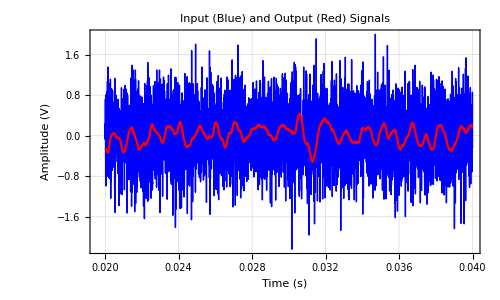

```mathematica
"■"; n1=10000; n2=20000;
ListLinePlot[{{ti[[n1;;n2]],x1[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],y1[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{{Blue,Thin},Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Blue) and Output (Red) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

Lets zoom in 10x more:

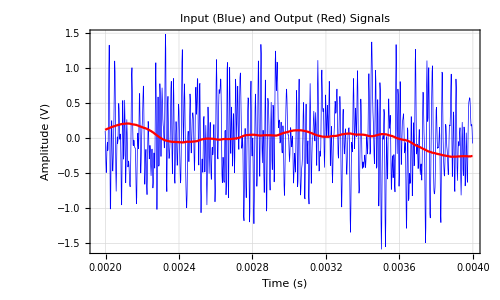

```mathematica
"■"; n1=1000; n2=2000;
ListLinePlot[{{ti[[n1;;n2]],x1[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],y1[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{{Blue,Thickness[0.001]},Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Blue) and Output (Red) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

The low pass nature of our Black Box is evident here. Clearly high frequencies in the input appear to be attenuated. The Black Box looks as though it is low pass.

Lets zoom in 10x more:

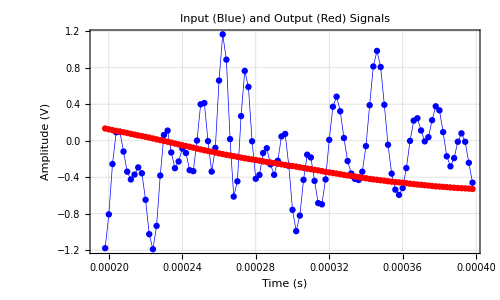

```mathematica
"■"; n1=100; n2=200;
Show[
ListLinePlot[{{ti[[n1;;n2]],x1[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],y1[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{{Blue,Thickness[0.001]},Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Blue) and Output (Red) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500],
ListPlot[{{ti[[n1;;n2]],x1[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],y1[[n1;;n2]]}ᵀ},PlotStyle->{Blue,Red}]]
```

Now we can see the individual data points.

#### Input and Output Signal Probability Density Functions

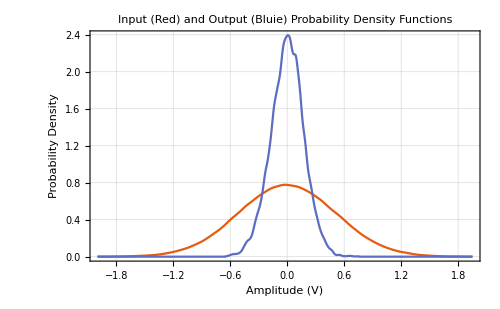

```mathematica
"■";
SmoothHistogram[{x1,y1},Automatic,"PDF",PlotRange->All,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Red) and Output (Bluie) Probability Density Functions",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Probability Density",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500]
```

We can see here that both the input and output probability densities appear Gaussian. This is a requirement of a  linear system but could occur with certain nonlinear systems.

We can compare the output probability density to a Gaussian probability density function having the same mean and standard deviation:

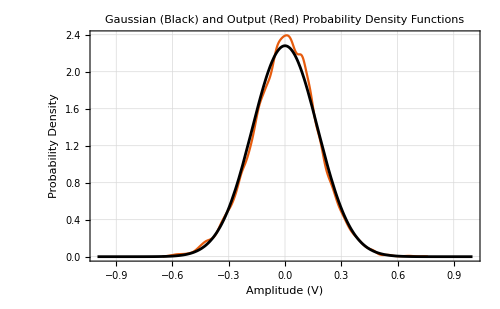

```mathematica
"■";  Show[
SmoothHistogram[y1,Automatic,"PDF",PlotRange->All,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Gaussian (Black) and Output (Red) Probability Density Functions",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Probability Density",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500],
Plot[PDF[NormalDistribution[Mean[y1],StandardDeviation[y1]],yy],{yy,-1,1},PlotStyle->Black]]
```

We can see that the output is remarkably Gaussian.
If the input to a linear dynamic system is Gaussian then the output will also be Gaussian. If the input is Gaussian and the output clearly non-Gaussian then that is a clear indication that the system is nonlinear. However the reverse is not true: if the input is non-Gaussian and the output is Gaussian it could still be a either a linear or  nonlinear system. Remember to distinguish a necessary condition from a necessary and sufficient condition.

#### Input and Output Signal Auto-Correlation Functions

Mathematica provides two methods to compute the auto-correlation function, called CorrelationFunction[] and ListCorrelate[].
CorrelationFunction[] returns a normalized auto-correlation function (the τ=0 term =1). We do not want this for subsequent system ID. Also CorrelationFunction[] is rather slow (“brute force” method) which does not exploit the FFT algorithm and furthermore cannot be used to compute the cross-correlation function which we need for system ID.
ListCorrelate[] returns the un-normalized auto- and cross-correlation functions and exploits the FFT algorithm which is very fast and essential for large values of n. It is best used when n is a power of 2 (as here) in order to fully exploit the benefits of the FFT approach.

We can see that the input auto-correlation function is that of a white noise signal.

When we use ListCorrelate we need to extract the m+1 values we want and divide by n to get biased Auto-Covariance Function values. 
Note that we could divide each correlation function value by n-k (where is the lag index) to give the unbiased estimate. However the unbiased estimate has larger estimation error than the biased estimate particularly for higher values of k.
In the following we show the effect of varying the length of the auto-correlation function:

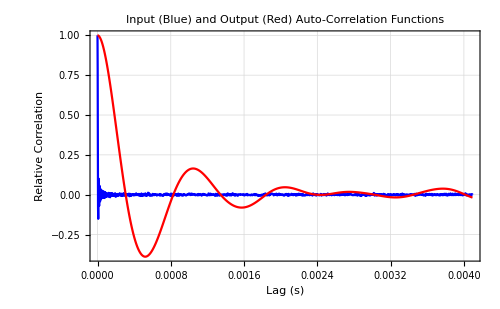

```mathematica
"■";  m=2^11;
τi=Range[0.0,(m-1) Δt,Δt];
cxx=ListCorrelate[x1,x1,{-1,1},0][[n;;n+m-1]]/n;
cyy=ListCorrelate[y1,y1,{-1,1},0][[n;;n+m-1]]/n;
cxx=cxx/cxx[[1]]; (* we normalize the auto-correlation function so that it starts at 1 *)
cyy=cyy/cyy[[1]]; (* we normalize the auto-correlation function so that it starts at 1 *)
ListLinePlot[{{τi,cxx}ᵀ,{τi,cyy}ᵀ},PlotRange->All,PlotStyle->{Blue,Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input (Blue) and Output (Red) Auto-Correlation Functions",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Relative Correlation",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500]
```

We can clearly see here that the input auto-correlation function (blue) has a spike at zero lag and then drops to zero fairly quickly and after a few oscillations remains at zero. This is to be expected when the input has a flat power spectrum up to some frequency. By contrast the output auto-correlation function (red) clearly has memory for its previous values and will therefor not have a flat power spectrum.
Note also that we need to make sure that the output auto-correlation function is computed out to a sufficiently high lag to ensure that it has “died” down enough. You also should make sure that the length, n, of the input signal is at least 10x the length, m,  of the auto-correlation function. In our case we have:

```mathematica
n
```

262144

and

```mathematica
m
```

2048

This is also a useful thing to know because it also suggests that if needed we could reduce n to 5,000 from 500,000 or so. This of course would result in a 100x shorter experiment.

#### Input and Output Power Spectra

The Fourier transform of the auto-correlation function is the power spectrum. We could determine the power spectrum by doing this. Alternatively we can estimate the power spectrum directly from the original input data using FFT methods. Note that we use Welches method which is available from the Wolfram Resource Function repository. Welches method requires that we divide the signal up in to overlapping segments of length nseg. The shorter the segment the more filtering of the spectra we get. The segment length also determines the spectral resolution (i.e., spacing between adjacent frequencies ( = first non-zero frequency).

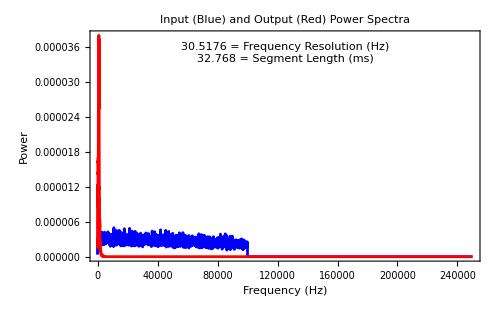

```mathematica
"■";  nseg=2^14;
xps=ResourceFunction["WelchSpectralEstimate"][x1,1/Δt,"SegmentSize"-> nseg,"Window"->HannWindow];
yps=ResourceFunction["WelchSpectralEstimate"][y1,1/Δt,"SegmentSize"-> nseg,"Window"->HannWindow];
ListPlot[{xps,yps},PlotRange->{All,All},Joined->True,PlotStyle->{Blue,Red},PlotLabel->"Input (Blue) and Output (Red) Power Spectra",
Frame->True,FrameLabel->{"Frequency (Hz)","Power"},GridLines->Full,ImageSize->500,
Epilog->{Black,Text[ 1/(nseg Δt) "= Frequency Resolution (Hz)",Scaled[{0.5,0.93}]],
Black,Text[  nseg Δt 1000. "= Segment Length (ms)",Scaled[{0.5,0.88}]]}]
```

Lets plot the power spectra on log axes:

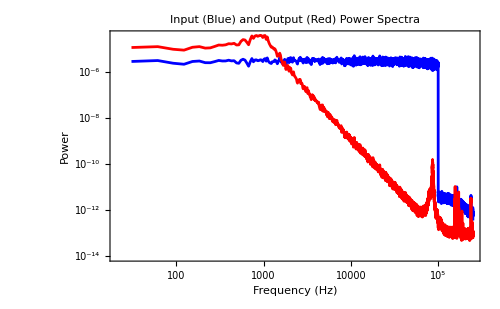

```mathematica
"■";  ListLogLogPlot[{xps,yps},PlotRange->{All,All},Joined->True,PlotStyle->{Blue,Red},PlotLabel->"Input (Blue) and Output (Red) Power Spectra",
Frame->True,FrameLabel->{"Frequency (Hz)","Power"},GridLines->Full,ImageSize->500]
```

Here we can see that the input power spectrum (blue)  is  flat up to 100 kHz  whereas the output is clearly attenuated above about 1 kHz. This is indicates that we have a low-pass system because the Black Box is passing low frequencies but attenuating high frequencies. Furthermore there seems to be a peak around 1 kHz which suggests that our low-pass Black Box system my be under-damped.
Note also that the output (red) rolls off at high frequencies with a slope of -4. This is what we expect when the system is second-order (power rolls off at 2 x system order). But then the roll off stops and seems to reach a lower limit. This is the noise floor. If there was no noise in the system and if our ADCs could resolve smaller voltages then the roll-off will keep on going down.

#### Linear System ID

Now that we have analyzed some major properties of the input and output we can proceed to determine a dynamic model of the Black Box itself.  We will carry out linear system identification (ID). In subsequent notes we will consider how to perform system ID on potentially nonlinear dynamic systems.

#### Input Output Cross-Correlation Function

So far we have computed the input and output auto-correlation functions which measure the degree to which a signal is correlated with itself. However we can apply the same concept between two signals to see the degree to which one signal (e.g., the output) may be correlated with another (e.g., the input). Such a correlation between two signals is called a cross-correlation function:

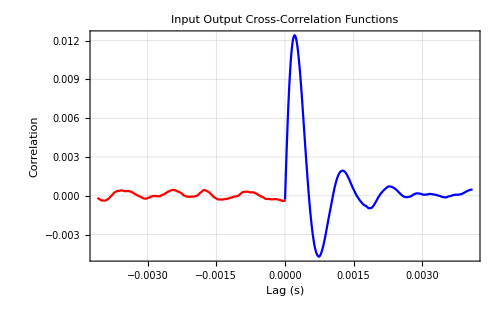

```mathematica
"■";  
τi=Range[0.0,(m-1) Δt,Δt];
cxx=ListCorrelate[x1,x1,{-1,1},0][[n;;n+m-1]]/n; (* input auto-correlation function *)
cyy=ListCorrelate[y1,y1,{-1,1},0][[n;;n+m-1]]/n; (* output auto-correlation function *)
cxy=ListCorrelate[x1,y1,{-1,1},0][[n;;n+m-1]]/n; (* input output cross-correlation fn *)
cyx=ListCorrelate[y1,x1,{-1,1},0][[n;;n+m-1]]/n; (* output input cross-correlation fn *)
ListLinePlot[{{τi,cxy}ᵀ,{-τi,cyx}ᵀ},PlotRange->All,PlotStyle->{Blue,Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Input Output Cross-Correlation Functions",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Correlation",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
ImageSize->500]
```

Unlike the auto-correlation function which is always symmetric the cross-correlation between x and y (blue) is different than between y and x (red). This is clearly seen above where the cross-correlation between y and x (red) is near zero. This will be the case for causal systems. However for system that can anticipate (like a living system) the cyx values may be non-zero.

#### Input-Output Cross-Power Spectrum

The Fourier transform of the cross-correlation function is the cross-power spectrum. We could determine the cross-power spectrum by doing this. Alternatively we can estimate the cross-power spectrum directly from the original input-output data using FFT methods:

```mathematica
"■";  nseg=2^14;
xyps=ResourceFunction["WelchSpectralEstimate"][x1,y1,1/Δt,"SegmentSize"->nseg,"Window"->HannWindow];
```

The cross-power spectrum values are complex. We will not plot it but will use it later to estimate the system frequency response function.

#### Estimate the System Impulse Response Function

We can estimate the system non-parametric impulse response function by de-convolving the input auto-correlation function from the input-output cross-correlation function. One way to do this is to use a special matrix called the Toeplitz matrix.

A Toeplitz matrix has a special structure:

```mathematica
"■";ToeplitzMatrix[{1,2,3,4,5}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5
2 | 1 | 2 | 3 | 4
3 | 2 | 1 | 2 | 3
4 | 3 | 2 | 1 | 2
5 | 4 | 3 | 2 | 1)

Note the particular symmetry of this matrix. We will form the Toeplitz matrix from the input auto-correlation function values.

#### Estimate the System Impulse Response Function via Toeplitz Matrix Inversion

This deconvolution may be implemented using a matrix equation involving the inverse of the Toeplitz matrix formed from the input auto-correlation function times the cross-correlation function. 
However this is a brute force approach and when the length, m, of cxx gets large then the Toeplitz matrix gets huge (m x m). Only use the following direct matrix inversion if m ≤ 2^9

```mathematica
(*Solve for impulse response *)
hi=1/Δt Inverse[ToeplitzMatrix[cxx]].cxy;  (* probably best not to execute this *)
```

A better way to perform these matrix operations is to use the Mathematica LinearSolve[] function:

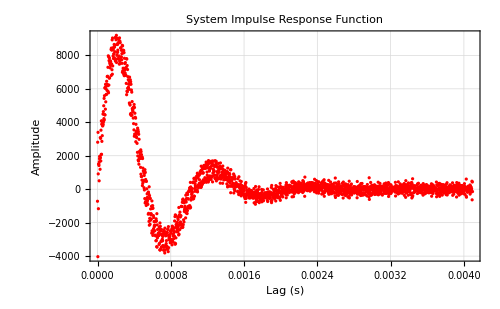

```mathematica
(*Solve for impulse response *)
"■"; hi=1/Δt LinearSolve[ToeplitzMatrix[cxx],cxy];
ListPlot[{τi,hi}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["System Impulse Response Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
ImageSize->500]
```

#### Estimate the System Impulse Response Function via SVD

Singular Value Decomposition (SVD) is together with the Fast Fourier Transform (FFT) is one of the most important algorithms developed. We can use it here to do a better job of performing the Toeplitz matrix inversion. An additional benefit is that we can get rid of small singular values (smaller than a threshold) that are likely to not contribute usefully to the impulse response function estimate.

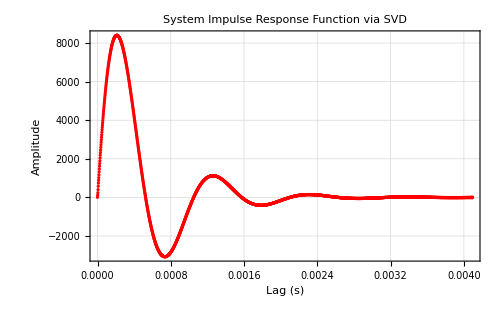

```mathematica
(* SVD with threshold *)(* Truncated SVD solution *)
"■"; {U,S,V}=SingularValueDecomposition[ToeplitzMatrix[cxx]];
threshold=0.1 Max[S]; (*Keep only significant singular values*)
Sinv=DiagonalMatrix[1/Max[#,threshold]&/@Diagonal[S]];
hSVD=1/Δt V.Sinv.Transpose[U].cxy;
ListPlot[{τi,hSVD}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["System Impulse Response Function via SVD",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
ImageSize->500]
```

The area under the system impulse response function should equal the system static gain. We can integrate the impulse response function to find the area under it. If the impulse response function was in the form of an equation then we could symbolically integrate it. However our estimate of the impulse response function is in non-parametric form (i.e., a list of numbers).

A crude way to do numerical integration is rectangular integration:

```mathematica
"■"; Δt Total[hSVD]
```

1.99905

Here we see that the area under the impulse response function (i.e., the static gain) is close to 2.

A better way to perform integration of such a non-parametric function is to first interpolate it with an interpolation function (here we use Interpolation[ ]) to yield a symbolic interpolation function and then to integrate this interpolation function symbolically.

```mathematica
"■"; f=Interpolation[{τi,hSVD}ᵀ,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
"■"; Integrate[f[t],{t,First[τi],Last[τi]}]
```

1.99904

We can see that the static gain predicted by this method is also very close to 2.

#### Predict Output

We will now predict the output using numerical convolution. But instead of using the x1 and y1 data we will use the x2 and y2 data. We want to make sure that our predictions are truly made from a separate data set.
 We now numerically convolve the measured input, x2, with the system as represented by the impulse response function, hSVD, to predict the output, ynp:

```mathematica
"■"; ynp=Δt ListConvolve[hSVD,x2,1];(* 1 tells the algorithm to make the input and output lengths the same *)
```

There are too many data points to plot so we will plot a small portion of the predicted output, ynp, and the measured output, y:

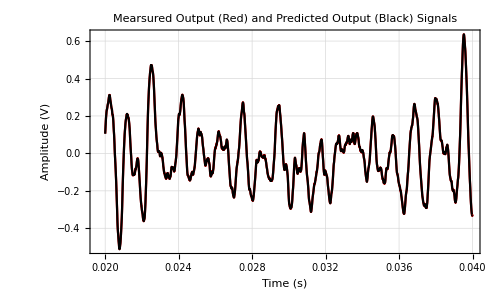

```mathematica
"■"; n1=10000; n2=20000;
ListLinePlot[{{ti[[n1;;n2]],y2[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],ynp[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{Red,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Mearsured Output (Red) and Predicted Output (Black) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

The prediction is so good it is difficult to distinguish the predicted output from the measured output.

#### Determine the residuals between measured output and predicted output from the non-parametric model

We can subtract the predicted output from the measured output to give the residuals (i.e., the output behavior that was not predicted). The residuals will be a combination of noise, higher-order dynamic behavior and nonlinearities. We will have to perform a nonlinear analysis to separate nonlinear behavior from measurement or system noise.

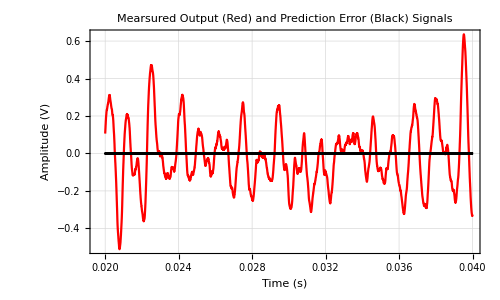

```mathematica
"■"; n1=10000; n2=20000;
ListLinePlot[{{ti[[n1;;n2]],y2[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],(y2[[n1;;n2]]-ynp[[n1;;n2]])}ᵀ},PlotRange->All,PlotStyle->{Red,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Mearsured Output (Red) and Prediction Error (Black) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

There is always a start up transient caused by the implicit assumption in convolution that the value of the input for t<0 is = 0. This causes an initial condition transient which often results in poor prediction for a length of the output equal to the time taken for the impulse response function to die down to zero. Lets look at this initial part of the predicted output:

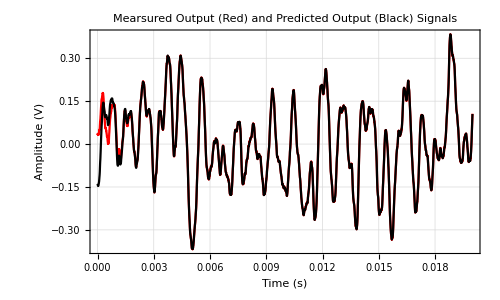

```mathematica
"■"; n1=1; n2=10000;
ListLinePlot[{{ti[[n1;;n2]],y2[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],ynp[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{Red,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Mearsured Output (Red) and Predicted Output (Black) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

Lets zoom in even further on this initial region:

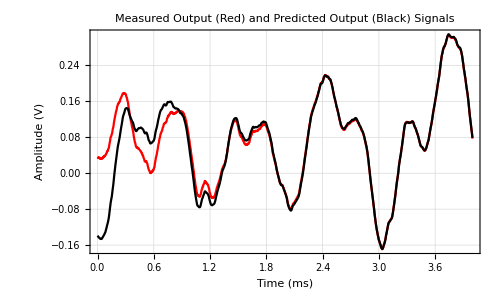

```mathematica
"■"; n1=1; n2=2000;
ListLinePlot[{{1000 ti[[n1;;n2]],y2[[n1;;n2]]}ᵀ,{1000 ti[[n1;;n2]],ynp[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{Red,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Measured Output (Red) and Predicted Output (Black) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (ms)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

We can see that the prediction error gets less as we increase time. If you look back at the estimated impulse response function you can see that it has “died down” to zero in about 3 ms. This is exactly how long it takes for the transient poor predictions to decay to near zero. For this reason is is common to trim off this initial artifact from any subsequent analyses. The number of samples we want to trim is:

```mathematica
"■"; nTrim=0.003/Δt
```

1500.

The prediction is almost perfect. The low-pass nature of the system is clear (the high frequencies in the input do not appear in the output).

#### % Variance Accounted For (%VAF)

It is useful to have a single measure of the degree to which our model (parametric or non-parametric) can predict the output for a given input. One such measure is the variance accounted for. It tells use the % of the output variation (variance) which is accounted for by the model. If every nuance in the output is predicted by a model than the %VAF = 100%. Conversely, if none of the output is predicted by the model the %VAF = 0. As a general rule we normally want to see the %VAF well above 75%. For example, if the %VAF = 80% the the 20% unaccounted for by the model is some combination of noise and nonlinearity (you can only find out how much is noise vs nonlinearity by doing a nonlinear analysis (e.g., nonlinear system ID). Here we compute the %VAF after trimming off the initial transient:

```mathematica
"■"; vafNP=100(1-Variance[(ynp-y2)[[nTrim;;All]]]/Variance[y2[[nTrim;;All]]])
```

99.9983

We have clearly almost completely predicted every variation in the Black Box output.

#### Analysis of Non-Parametric Model Residuals

It is useful to look at the properties of the non-parametric model residuals. The residuals  are a combination of un-modeled linear and non-linear dynamics, measurement noise,  etc.

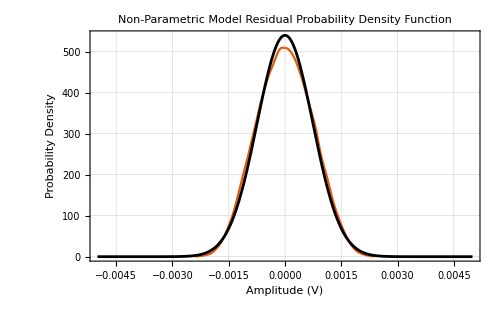

```mathematica
"■";  res=(ynp-y2)[[nTrim;;All]];
res=res-Mean[res]; (* remove the mean offset *)
Show[
SmoothHistogram[res,Automatic,"PDF",PlotRange->All,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Non-Parametric Model Residual Probability Density Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Probability Density",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500],
Plot[PDF[NormalDistribution[Mean[res],StandardDeviation[res]],yy],{yy,-0.005,0.005},PlotStyle->Black]]
```

Here we can see that the residuals are Gaussian. This is very common and indeed justifies the use of the least squares fitting we used (because least squares assumes that the errors are Gaussian).

We can also look at the auto-correlation function of the residuals:

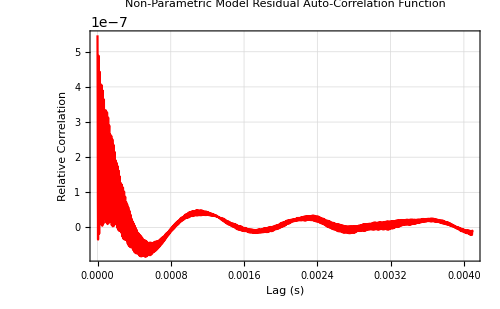

```mathematica
"■";  m=2^11; nn=Length[res];
τi=Range[0.0,(m-1) Δt,Δt];
crr=ListCorrelate[res,res,{-1,1},0][[nn;;nn+m-1]]/nn;
ListLinePlot[{τi,crr}ᵀ,PlotRange->All,PlotStyle->{Blue,Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Non-Parametric Model Residual Auto-Correlation Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Relative Correlation",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500]
```

Ideally the residual auto-correlation function should be that of a white noise signal (i.e., a spike at zero lag and zero elsewhere). It is not. This indicates that there is probably a very small additional higher order dynamic component and/or a very small dynamic nonlinearity we have not modeled. It is so small that we are not going to worry about it.
We can also look at the power spectrum of the residuals:

```mathematica
"■";  nseg=2^14;
rps=ResourceFunction["WelchSpectralEstimate"][res,1/Δt,"SegmentSize"-> nseg,"Window"->HannWindow];
```

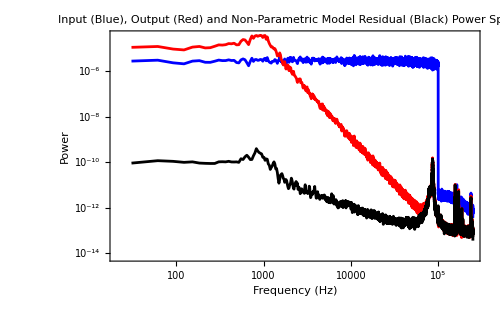

```mathematica
"■";  ListLogLogPlot[{xps,yps, rps},PlotRange->{All,All},Joined->True,PlotStyle->{Blue,Red,Black},PlotLabel->"Input (Blue), Output (Red) and Non-Parametric Model Residual (Black) Power Spectra",
Frame->True,FrameLabel->{"Frequency (Hz)","Power"},GridLines->Full,ImageSize->500]
```

Clearly the residuals are not white but as expected they overlap at high frequencies (<50 kHz) with the noise floor of the output.

#### Estimate Frequency Response Function (Bode plot)

We now ask if we can estimate the Black Box frequency response function. There many ways we can do this. One way is to do what we have done before which is run a separate experiment in which we sweep a sinusoidal input from low frequency (e.g., 10 Hz) to a suitably high frequency (e.g., 100 kHz). It would be nice if we could predict the frequency response from our existing input output data set. There are two basic ways we can do this. The first is to Fourier transform the impulse response function. The other is to use the input power spectrum that we have already computed together with the cross-power spectrum which we also computed. Indeed the system frequency response function, fr, may be estimated by dividing the input power spectrum by the cross-power spectrum:

```mathematica
"■";
freq=xps[[All,1]];
fr=xyps[[All,2]]/xps[[All,2]];
frGain=Abs[fr];
frPhase=360/(2π)ResourceFunction["PhaseUnwrap"][Arg[fr]];
```

```mathematica
"■";  Quiet[ResourceFunction["PlotGrid"][
{{ListLogLogPlot[{freq,frGain}ᵀ,Joined->True, PlotStyle->Red,PlotLabel->"Bode Plot",
Frame->True,FrameLabel->{"Frequency (Hz)","Gain"},GridLines->Full]},
{ListLogLinearPlot[{freq,frPhase}ᵀ,PlotRange->{All,{-200,20}},Joined->True, PlotStyle->Red,Frame->True,FrameLabel->{"Frequency (Hz)","Phase (deg)"},GridLines->Full]}},AspectRatio->1.2,ImageSize->500]]
```

-Graphics-

#### Coherence Squared Function

The non-parametric frequency response function (like its inverse Fourier transform, the non-parametric system impulse response function) is the best linear dynamic model between the input and the output (remember that at this point we have not restricted the model order in any way). We would like to know how well the frequency response model predicts the output as a function of frequency. The coherence squared function, frCohSq, does exactly this. Indeed just as the percentage variance accounted for (%VAF) gives the overall % with which the output variation is predicted by the input, the % coherence squared  function gives the % variance accounted for at each frequency.  

Coherence squared values of less that 50% are considered to be low in engineering and physics.

There are two ways in which the % coherence squared may be low: 
1. is because of nonlinearities (often systems may be found to be linear over a range of input frequencies but then behave nonlinearly outside this range); 
2. is because at certain frequencies the additive (“measurement”) noise to the output may be higher at some frequencies than others.
It is not possible to tell just by looking a the coherence squared function whether low coherence squared values are due to noise or nonlinearities.

```mathematica
"■";frCohSq=Abs[xyps[[All,2]]]^2/(xps[[All,2]] yps[[All,2]]);
```

```mathematica
"■"; Quiet[ResourceFunction["PlotGrid"][
{{ListLogLogPlot[{freq,frGain}ᵀ,PlotRange->{All,{0.0001,10}},Joined->True, PlotStyle->Red,PlotLabel->"Frequency Response",
Frame->True,FrameLabel->{"Frequency (Hz)","Gain"},GridLines->Full]},
{ListLogLinearPlot[{freq,frPhase}ᵀ,PlotRange->{All,{-200,20}},Joined->True, PlotStyle->Red,Frame->True,FrameLabel->{"Frequency (Hz)","Phase (deg)"},GridLines->Full]},
{ListLogLinearPlot[{freq,frCohSq}ᵀ,PlotRange->{All,{0,1.2}},Joined->True, PlotStyle->Red,Frame->True,FrameLabel->{"Frequency (Hz)","Squared Coherence"},GridLines->Full]}},
AspectRatio->1.2,ImageSize->500]]
```

-Graphics-

This shows that the squared coherence is high at low frequencies and much lower at high frequencies (above 30 kHz or so). There is no point fussing about frequency response function gain and phase values over a band of frequencies if the squared coherence over that band of frequencies is low.
When parametric transfer function models are fitted to nonparametric frequency response models the squared coherence can be used as the weights in a weighted least-squares fit. In this way gain and phase values at frequencies where the squared coherence is low have less effect on the fit than values at frequencies where the squared coherence is high.

#### Consideration of Model Order

The high frequency roll-off gives a clue as to model order. When plotting on Log Log axes the Bode gain of a simple low-pass system should roll off with a slope equal to minus the system order. For example if the order is 2 then the high frequency asymptotic roll-off slope should be -2 (i.e. the high frequency system gain becomes 100 x less as the frequency in increased 10 x). The colored “roll-off” lines shown on the gain part of the Bode plot below have slopes of -1 (cyan), -2 (blue), and -3 (brown). The blue line is closest to the measured data and so we conclude that the system is second-order. This is confirmed by looking at the phase part of the Bode plot. The difference in value between the asymptotic low frequency phase value (0 deg here) and the asymptotic high frequency phase value will be -90 times the system order. In our case this phase difference is 180 deg which confirms that we have a second-order system. 

Note that the asymptotic low frequency phase value will be 180 deg rather than 0 deg if the overall static gain is negative. So in this case we can see that the overall gain of the Sallen-Key filter is positive because the low frequency phase starts at 0 and in addition it looks as though the value of the static gain, α, (i.e. its asymptotically low frequency gain value) is 2. This can be seen in the plot below.

The cutoff frequency, ω,  will occur when the phase is half way between the low and high frequency asymptotes (-90 here). In the plot below a vertical black line has been drawn through this half way point in the phase part of the Bode plot and extended up in to the gain part of the Bode plot. This line should intersect the black horizontal asymptotic low frequency gain line and the colored high frequency roll-off line extrapolated back to lower frequencies. See if this is indeed the case once the static gain, α, has been adjusted:

```mathematica
"■"; cutoffFreq=InverseFunction[Interpolation[{freq,frPhase}ᵀ,InterpolationOrder->1]][-90]
```

997.471

So we can see that the natural frequency (cut-off frequency) is close to 1,000 Hz and the static gain is close to 2.

```mathematica
"■"; Manipulate[
cutoffFreq=InverseFunction[Interpolation[{freq,frPhase}ᵀ,InterpolationOrder->1]][-90];(* finds frequency at which interpolated phase is -90 deg *)
Column[
{
ListLogLogPlot[{
{freq,frGain}ᵀ,
{{10,α},{20000,α}},
{{cutoffFreq,α},{100 cutoffFreq,0.01 α}},
{{cutoffFreq,α},{100 cutoffFreq,0.0001 α}},
{{cutoffFreq,α},{100 cutoffFreq,0.000001 α}},
{{cutoffFreq,0.0001},{cutoffFreq,2}}},
PlotRange->{{10, 100000},{0.0001,10}},
Frame->True,Joined->{False,True,True,True,True,True,True},PlotStyle->{Red,Black,Cyan,Blue,Brown,Black},LabelStyle->{14,Black},PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->500,
Epilog->
{Black,Text[cutoffFreq "Hz",Scaled[{0.53,0.95}]],
Cyan,Text["-1" ,Scaled[{0.8,0.7}]],
Blue,Text["-2" ,Scaled[{0.66,0.7}]],
Brown,Text["-3" ,Scaled[{0.55,0.7}]]}],
ListLogLinearPlot[{
{freq,frPhase}ᵀ,
{{10,0},{10^5,0}},
{{10,-90},{10^5,-90}},
{{10,-180},{10^5,-180}},
{{cutoffFreq,-200},{cutoffFreq,10}}},
PlotRange->{{10, 100000},{-200,10}},
Frame->True,Joined->{False,True,True,True,True},
PlotStyle->{Red,{Black,Dashed},Black,{Black,Dashed},Black},LabelStyle->{14,Black},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->500,
Epilog->
{Black,Text["-90 deg" ,Scaled[{0.1,0.56}]],
Black,Text["-180 deg" ,Scaled[{0.1,0.14}]]}]
},
Spacings->0],
{{α,0.5,"Static gain α"},0.1,3.0,0.1,Appearance->"Labeled"},
ControlPlacement->Top]
```

It can be seen that the cut-off frequency (natural frequency), ω, is very close to 1 kHz (or 2π 1000 rad/s).

A simple low-pass, second-order system is defined by three parameters: the static gain, α, the natural frequency, ω, and the damping parameter, ζ.  As yet we have not estimated the value of the damping parameter but from experience it looks as though it is somewhere less than 0.5 but greater than 0.1.

In the following we allow all three parameters to be adjusted to give a feel for the effect each has on the features of the Bode plot.

#### Fit a Parametric Second-Order Transfer Function Model by Hand

As shown before the general equation for the transfer function of a second-order low-pass filter is:

```mathematica
"■"; H[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2);
```

where the static gain is α, the natural frequency (in radians/s) is ω, and the damping parameter is ζ.

Lets fit the transfer function by hand. Remember that the coherence squared function values are low at higher frequencies so you should be more careful in fitting low frequency values than those at high frequencies:

```mathematica
"■"; Manipulate[
Column[
{Show[
ListLogLogPlot[{freq,frGain}ᵀ,PlotRange->{{10, 100000},{0.00007,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->500],
LogLogPlot[Abs[H[ⅈ f 2 π,α,2π ω,ζ]],{f,10,100000},PlotStyle->Black]],
Show[
ListLogLinearPlot[{freq,frPhase}ᵀ,PlotRange->{{10, 100000},{-200,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->500],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,α,2π ω,ζ]],{f,10,100000},PlotStyle->Black]]},
Spacings->0],
{{α,1, "Static gain α"},1.0,3.0,0.1,Appearance->"Labeled"},
{{ω,600.0,"Natural frequency ω (Hz)"},500.0 ,2000.0 ,10,Appearance->"Labeled"},
{{ζ,1,"Damping parameter ζ"},0.1,2.0,0.01,Appearance->"Labeled"},
ControlPlacement->Top]
```

Note that the natural frequency, ω, is in radians/s (divide by 2 π to get the natural frequency in Hz).

Note the values of the three parameters.

#### Fit a Parametric Second-Order Transfer Function Model by Nonlinear Minimization

Lets now use a nonlinear minimization technique to fit the model to the data (actually we fit to just the gain data: it would be better to fit to both the gain and phase data simultaneously):

```mathematica
"■"; αα=2; ωω=1000 2 π; ζζ=0.3;
nlm=NonlinearModelFit[{freq,frGain}ᵀ,Abs[H[ⅈ f,α,ω,ζ]],{{α,αα},{ω,ωω},{ζ,ζζ}},f, Method->"LevenbergMarquardt",AccuracyGoal->2];
nlm["BestFitParameters"]
{αα,ωω,ζζ}={α,ω,ζ}/.nlm["BestFitParameters"];
```

{α→2.00228,ω→1001.28,ζ→0.306671}

Note that here the natural frequency is in Hz rather than rad/s.

Also note that the system static gain, α, natural frequency, ω, and damping parameter, ζ, are very close to 2, 1000 Hz, and 0.3 respectively. Indeed as we will see below this particular Black Box was designed to have exactly these parameters.

```mathematica
"■"; {αα,ωω,ζζ}={α,ω,ζ}/.nlm["BestFitParameters"];
```

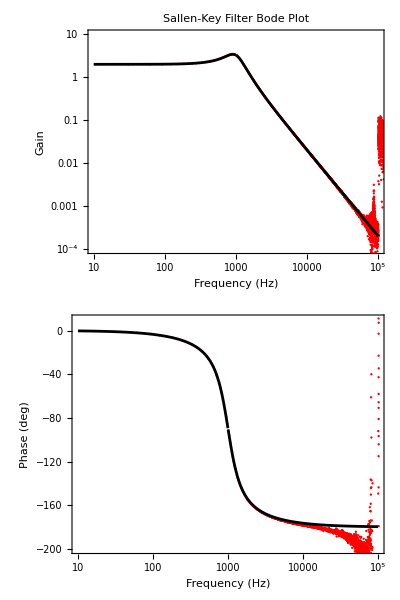

```mathematica
"■";
Column[
{Show[
ListLogLogPlot[{freq,frGain}ᵀ,PlotRange->{{10, 100000},{0.0001,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600],
LogLogPlot[Abs[H[ⅈ f 2 π,αα,ωω 2 π,ζζ]],{f,10,100000},PlotStyle->Black]],
Show[
ListLogLinearPlot[{freq,frPhase}ᵀ,PlotRange->{{10, 100000},{-200,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,αα,ωω 2 π,ζζ]],{f,10,100000},PlotStyle->Black]]},
Spacings->0]
```

Lets look at the fit over the range of frequencies (e.g., 10 Hz to 20 kHz (i.e., the audio range)) for which the coherence squared function values are reasonably high:

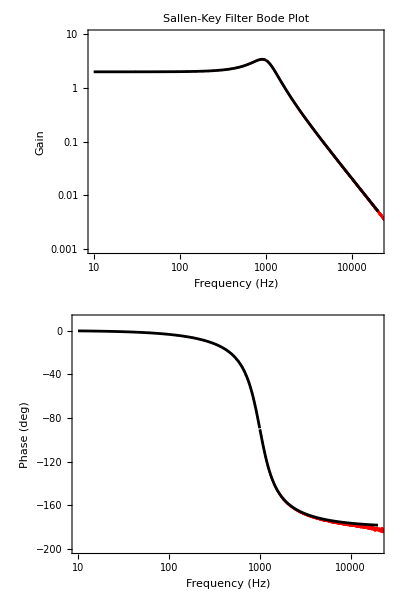

```mathematica
"■";
Column[
{Show[
ListLogLogPlot[{freq,frGain}ᵀ,PlotRange->{{10, 20000},{0.001,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Sallen-Key Filter Bode Plot",
FrameLabel->{"Frequency (Hz)","Gain"},AspectRatio->0.5,ImagePadding->{{60,10},{2,0}},ImageSize->600],
LogLogPlot[Abs[H[ⅈ f 2 π,αα,ωω 2 π,ζζ]],{f,10,20000},PlotStyle->Black]],
Show[
ListLogLinearPlot[{freq,frPhase}ᵀ,PlotRange->{{10, 20000},{-200,10}},
Frame->True,PlotStyle->Red,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
FrameLabel->{"Frequency (Hz)","Phase (deg)"},AspectRatio->0.5,ImagePadding->{{60,10},{50,10}},ImageSize->600],
LogLinearPlot[360/(2*Pi)Arg[H[ⅈ f 2 π,αα,ωω 2 π,ζζ]],{f,10,20000},PlotStyle->Black]]},
Spacings->0]
```

We can see that over this range the fit of the second-order transfer function to the frequency response estimates is almost perfect.

#### Fit a Parametric Second-Order Impulse Response Function Model

The general equation for the transfer function of a second-order low-pass filter is:

```mathematica
"■"; H[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2);
```

where the static gain is α, the natural frequency (in radians/s) is ω, and the damping parameter is ζ.

The system parametric impulse response function is simply the inverse Laplace transform of this parametric transfer function:

```mathematica
"■"; InverseLaplaceTransform[(α ω^2)/(s^2+2ζ ω s+ω^2),s,τ]
```

-((ⅇ^(τ (-ζ ω-√((-1+ζ^2) ω^2)))-ⅇ^(τ (-ζ ω+√((-1+ζ^2) ω^2)))) α ω^2)/(2 √((-1+ζ^2) ω^2))

In defining the general impulse response function of this second-order system we need to treat the case when ζ=1 as a special case in order to avoid a divide by 0 error.

```mathematica
"■"; InverseLaplaceTransform[(α ω^2)/(s^2+2ω s+ω^2),s,τ]
```

ⅇ^(-τ ω) α τ ω^2

We can now define a function which returns the impulse response function for different values of α, ζ, and ω :

```mathematica
h[τ_,α_,ζ_,ω_]:=
If[ζ==1,
InverseLaplaceTransform[(α ω^2)/(s^2+2ω s+ω^2),s,τ],
InverseLaplaceTransform[(α ω^2)/(s^2+2ζ ω s+ω^2),s,τ]]
```

However you will find that repeated evaluations of this function is too slow because the inverse Laplace transforms have to be redone every time it is evaluated. Better to do the following:

```mathematica
h[τ_,α_,ζ_,ω_]:=
If[ζ==1.0,
Re[ⅇ^(-τ ω) α τ ω^2],
Re[-((ⅇ^(τ (-ζ ω-√((-1+ζ^2) ω^2)))-ⅇ^(τ (-ζ ω+√((-1+ζ^2) ω^2)))) α ω^2)/(2 √((-1+ζ^2) ω^2))]]
```

Note that for negative value of τ this function will give non-zero results. This can be “fixed” by multiplying by the Heaviside Theta function (which is 0 when τ<0). This is the even better function:

```mathematica
"■";h[τ_,α_,ζ_,ω_]:=(
If[α==0.0, α=0.001];
If[ζ<=0.0, ζ=0.001];
If [ω<=0.0,ω=0.001];
If[ζ==1.0,
Re[ⅇ^(-τ ω) α τ ω^2]HeavisideTheta[τ],
Re[-((ⅇ^(τ (-ζ ω-√((-1+ζ^2) ω^2)))-ⅇ^(τ (-ζ ω+√((-1+ζ^2) ω^2)))) α ω^2)/(2 √((-1+ζ^2) ω^2))]HeavisideTheta[τ]])
```

#### Fit by Hand

```mathematica
"■"; Manipulate[
Show[
Plot[h[τ,α,ζ, 2 π ω],{τ,0,0.005},PlotRange->{All,{-4000,10000}},PlotStyle->Black,
Frame->True,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Black Box Impulse Response",
FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,ImageSize->500],
ListPlot[{τi,hSVD}ᵀ,PlotRange->All,PlotStyle->Red]],
{{α,1,"Static gain α"},0.5,3.0,0.1,Appearance->"Labeled"},
{{ω,600.0,"Natural frequency ψ (Hz)"},500.0 ,2000.0,10,Appearance->"Labeled"},
{{ζ,1,"Damping ζ"},0.1,2.0,0.02,Appearance->"Labeled"}]
```

#### Fit a Parametric Model Using Nonlinear Minimization

The estimated system impulse response function is a nonparametric model with no restriction on model order. We now want to fit a second-order model by minimizing the sum of squared differences between the nonparametric and parametric models:

For an equation of this complexity it is unlikely that a direct or analytic approach may be taken to estimate the "best fit" parameters. We therefore will use iterative method to estimate the parameters which minimize the least squares objective function. Because our equation has nonlinear terms in it, we need to use what is called a nonlinear minimization technique. Mathematica possess some very sophisticated nonlinear minimization techniques. We will use a very powerful technique called the Levenberg-Marquardt nonlinear minimization algorithm which is one of a number available in Mathematica's NonlinearModelFit function. In order to help the nonlinear minimization method achieve its goal of finding the parameters which minimize the objective function we need to supply some initial parameter estimates (ααα, ζζζ, ωωω) obtained from the fit we did by hand above:

```mathematica
"■";ααα=2; ζζζ=0.3; ωωω=2π 1000; (* initial parameter guesses *)
```

```mathematica
"■";RootMeanSquare[h[τi,ααα,ζζζ,ωωω]-hSVD]
```

25.5338

```mathematica
"■"; nlm=NonlinearModelFit[{τi,hSVD}ᵀ,{h[τ,α,ζ,ω],α>0,ζ>0,ω>0},{{α,ααα},{ζ,ζζζ},{ω,ωωω}},τ];
```

```mathematica
(*"■"; nlm=NonlinearModelFit[{τi,hnpm}ᵀ,h[τ,α,ζ,ω,0.1],{α,ζ,ω},τ]*)
```

The following are all the statistical measures available following the least squares fit:

```mathematica
nlm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVA,BestFitAround,BestFitDataAround,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,Weights,EstimatedVariance,FitCurvature,FitResiduals,Function,TabularFunction,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictions,MeanPredictionBands,ParameterEstimates,ParameterConfidenceRegion,ParameterBias,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictions,SinglePredictionBands,StandardizedResiduals,StudentizedResiduals}

```mathematica
"■"; nlm["BestFitParameters"]
```

{α→2.0003,ζ→0.304631,ω→6281.31}

```mathematica
"■"; nlm["RSquared"]
```

0.999992

Note that the three parameters we have estimated are almost exactly those used in the original simulation.

```mathematica
"■"; {ααα,ζζζ,ωωω}={α,ζ,ω}/.nlm["BestFitParameters"];
RootMeanSquare[h[τi,ααα,ζζζ,ωωω]-hSVD](* rms error after nonlinear least squares fit *)
```

6.51219

```mathematica
"■"; {ααα,ζζζ,ωωω}
```

{2.0003,0.304631,6281.31}

We can now compare the estimated parametric impulse response function with the original calculated nonparametric impulse response function

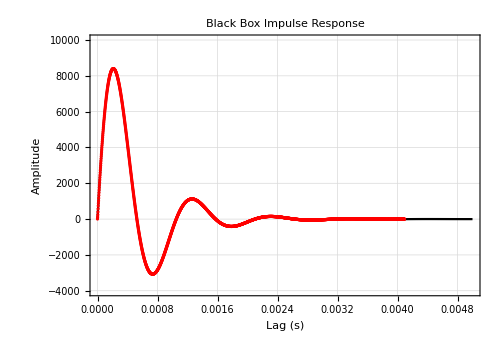

```mathematica
"■"; Show[
Plot[h[τ,ααα,ζζζ, ωωω],{τ,0,0.005},PlotRange->{All,{-4000,10000}},PlotStyle->Black,
Frame->True,LabelStyle->{14,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->"Black Box Impulse Response",
FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.7,ImageSize->500],
ListPlot[{τi,hSVD}ᵀ,PlotRange->All,PlotStyle->Red]]
```

As we can see the fit is remarkably good. We have reduced the number of parameters in our models from the non-parametric model:

```mathematica
Length[hSVD]
```

2048

to the 3 parameters, α, ω, and ζ of out parametric second-order model.

#### Predict Output

We can now re-predict our output but now using the 3 parameter parametric second-order model.
We numerically convolve the measured input, x2, with the system as represented by the second-order parametric impulse response function, h, to predict the output, yp. Note that we use x2 as input and not the training data, x1.

 We need to sample the parametric impulse response function to a version suitable for numeric convolution:

```mathematica
"■"; yp=Δt ListConvolve[h[τi,ααα,ζζζ, ωωω],x2,1];(* 1 tells the algorithm to make the input and output lengths the same *)
```

There are too many data points to plot so we will plot a small portion of the predicted output, yp, and the measured output, y:

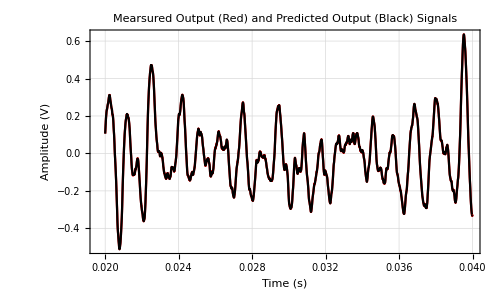

```mathematica
"■"; n1=10000; n2=20000;
ListLinePlot[{{ti[[n1;;n2]],y2[[n1;;n2]]}ᵀ,{ti[[n1;;n2]],yp[[n1;;n2]]}ᵀ},PlotRange->All,PlotStyle->{Red,Black},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Mearsured Output (Red) and Predicted Output (Black) Signals",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

As before the prediction is so good it is difficult to distinguish the predicted output from the measured output.

We can now determine the %VAF for this second-order model prediction:

```mathematica
"■"; vafP=100(1-Variance[(yp-y2)[[nTrim;;All]]]/Variance[y2[[nTrim;;All]]])
```

99.9978

Compare this with the %VAF we obtained when we made the non-parametric prediction:

```mathematica
"■"; vafNP
```

99.9983

As expected the 1025 parameter nonparametric prediction %VAF is higher than the 3 parameter second-order model %VAF but by only a trivial percentage:

```mathematica
"■"; vafNP-vafP
```

0.000443829

So we are justified in choosing the 3 parameter second-order model over the non-parametric model because we love powerful yet simple models.

#### Analysis of Parametric Model Residuals

It is useful to look at the properties of the parametric model residuals. The residuals  are a combination of un-modeled linear and non-linear dynamics, measurement noise,  etc.

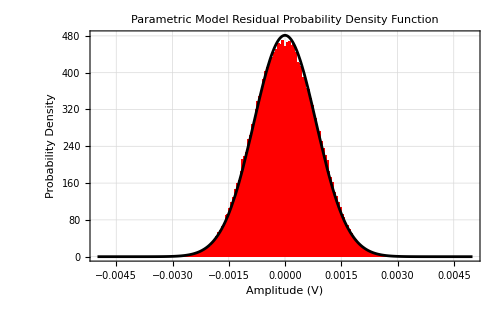

```mathematica
"■";  res=(yp-y2)[[nTrim;;All]];
res=res-Mean[res]; (* remove the mean offset *)
Show[
Histogram[res,{-0.005,0.005,0.00005},"PDF",PlotRange->All,
PlotTheme->{"Scientific","Grid"},ChartStyle->Red,
PlotLabel->Style["Parametric Model Residual Probability Density Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Amplitude (V)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Probability Density",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500],
Plot[PDF[NormalDistribution[Mean[res],StandardDeviation[res]],yy],{yy,-0.005,0.005},PlotStyle->Black]]
```

Here we can see that the residuals are Gaussian. This is very common and indeed justifies the use of the least squares fitting we used (because least squares assumes that the errors are Gaussian).

We can also look at the auto-correlation function of the residuals:

```mathematica
Length[crr]
```

2048

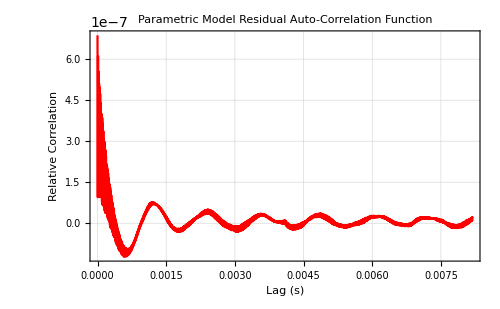

```mathematica
"■";  m=2^12; nn=Length[res];
τi=Range[0.0,(m-1) Δt,Δt];
crr=ListCorrelate[res,res,{-1,1},0][[nn;;nn+m-1]]/nn;
ListLinePlot[{τi,crr}ᵀ,PlotRange->All,PlotStyle->{Blue,Red},
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Parametric Model Residual Auto-Correlation Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Lag (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Relative Correlation",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],ImageSize->500]
```

Ideally the residual auto-correlation function should be that of a white noise signal (i.e., a spike at zero lag and zero elsewhere). It is not. This indicates that there is probably a very small additional higher order dynamic component and/or a very small dynamic nonlinearity we have not modeled. It is so small that we are not going to worry about it.
We can also look at the power spectrum of the residuals:

```mathematica
"■";  nseg=2^14;
rps=ResourceFunction["WelchSpectralEstimate"][res,1/Δt,"SegmentSize"-> nseg,"Window"->HannWindow];
```

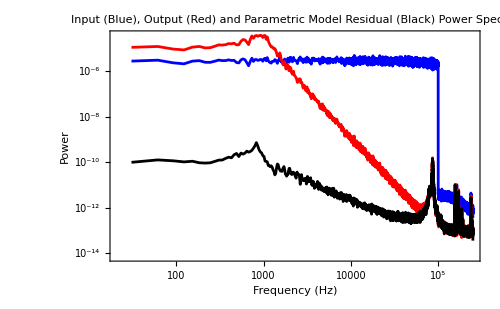

```mathematica
"■";  ListLogLogPlot[{xps,yps, rps},PlotRange->{All,All},Joined->True,PlotStyle->{Blue,Red,Black},PlotLabel->"Input (Blue), Output (Red) and Parametric Model Residual (Black) Power Spectra",
Frame->True,FrameLabel->{"Frequency (Hz)","Power"},GridLines->Full,ImageSize->500]
```

Clearly the residuals are not white but as expected they overlap at high frequencies (<50 kHz) with the noise floor of the output.

#### Parameter Sensitivity Functions

We would like some way to check that the parameters in our parametric second-order model are important. There is always the possibility that one or more parameter is making very little contribution to the fit. Parameter sensitivity functions reveal the degree to which variation in a parameter effect the function fit. They are calculated by holding all but one of the parameters at their best fit values while the remaining parameter is varied about its best fit value. If there is little increase in the sum of squares error (or what ever the objective function measure is) then this suggests that the parameter is unimportant and should be somehow removed from the function. If a parameter is near some physically meaningful value then the parameter sensitivity can show you that making a small change in the parameter may lead to its replacement as a free parameter by a fixed value. For example consider the power function:       y = ax^b 
when b is near 0 then you may be justified in eliminating the exponent b parameter and the variable x and setting     y = a, or
when b is near 0.5 then you may be justified in changing the exponent b parameter to the constant, 0.5, and setting    y = ax^0.5 =  a√x, or
when b is near 1 then you may be justified eliminating the exponent b parameter and setting    y = ax , or
when b is near 2 then you may be justified in changing the exponent b parameter to the constant, 2,  setting    y = ax^2 , or
etc

To generate the parameter sensitivity functions we need to computer the objective function (sum of squared prediction error in our case). Lets create a function for this:

```mathematica
"■"; errorSS[ααα_,ζζζ_, ωωω_]:=Total[((Δt ListConvolve[h[τi,ααα,ζζζ, ωωω],x2,1]-y2)^2)[[nTrim;;All]]]
```

Lets now look at the 3 parameter sensitivity functions:

```mathematica
errorSS[2,0.3,2 π 1000]
```

35.5584

```mathematica
{ααα,ζζζ, ωωω}
```

{2.0007,0.307533,6285.97}

#### Static Gain, α, Parameter Sensitivity Function

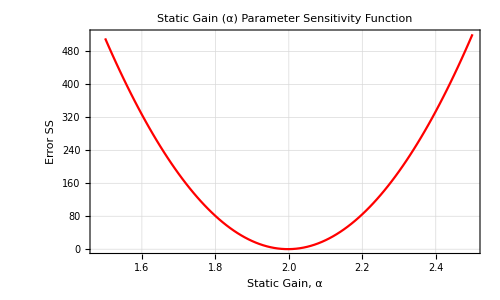

```mathematica
"■"; αVals=Range[1.5,2.5,0.01];
αSS=Table[errorSS[αααα,ζζζ, ωωω],{αααα,αVals}];
ListLinePlot[{αVals,αSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Static Gain (α) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Static Gain, α",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

Lets zoom in:

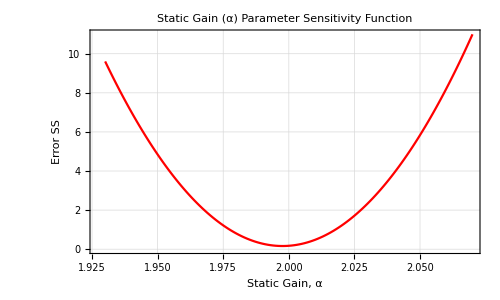

```mathematica
"■"; αVals=Range[1.93,2.07,0.001];
αSS=Table[errorSS[αααα,ζζζ, ωωω],{αααα,αVals}];
ListLinePlot[{αVals,αSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Static Gain (α) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Static Gain, α",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

So we can see that the static gain parameter, α, is important but we do not lose much by setting it to be 2.

#### Damping, ζ, Parameter Sensitivity Function

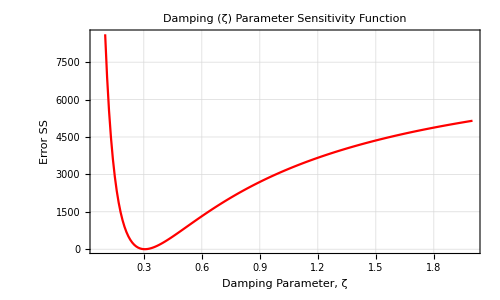

```mathematica
"■"; ζVals=Range[0.1,2,0.01];
ζSS=Table[errorSS[ααα,ζζζζ, ωωω],{ζζζζ,ζVals}];
ListLinePlot[{ζVals,ζSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Damping (ζ) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Damping Parameter, ζ",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

So we can see that the damping parameter, ζ, is important and fairly sharp degradation in the SS as we move away from the optimal value. Lets zoom in on the optimal value:

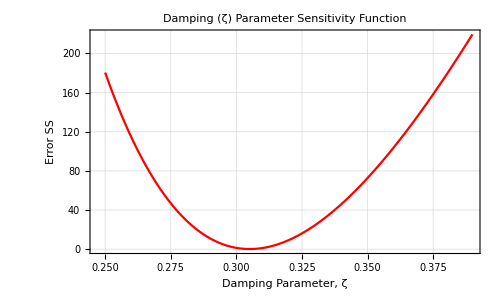

```mathematica
"■"; ζVals=Range[0.25,0.39,0.001];
ζSS=Table[errorSS[ααα,ζζζζ, ωωω],{ζζζζ,ζVals}];
ListLinePlot[{ζVals,ζSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Damping (ζ) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Damping Parameter, ζ",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

We can see that we could set ζ = 0.3 without much loss of fit.

#### Natural Frequency, ω, Parameter Sensitivity Function

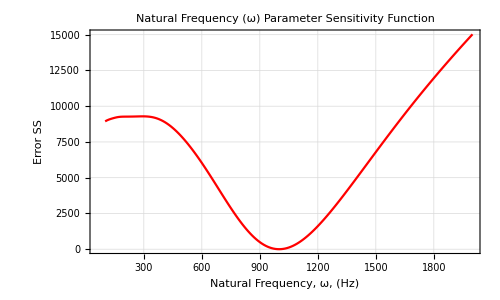

```mathematica
"■"; ωVals=Range[100,2000,10];
ωSS=Table[errorSS[ααα,ζζζ, 2π ωωωω],{ωωωω,ωVals}];
ListLinePlot[{ωVals,ωSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Natural Frequency (ω) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Natural Frequency, ω, (Hz)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

So we can see that the natural frequency parameter, ω, is important and fairly sharp degradation in the SS as we move away from the optimal value. Lets zoom in on the optimal value:

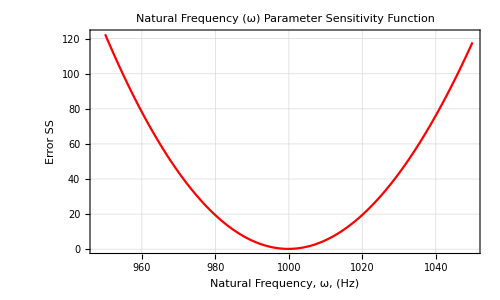

```mathematica
"■"; ωVals=Range[950,1050,1];
ωSS=Table[errorSS[ααα,ζζζ, 2π ωωωω],{ωωωω,ωVals}];
ListLinePlot[{ωVals,ωSS}ᵀ,PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},
PlotLabel->Style["Natural Frequency (ω) Parameter Sensitivity Function",FontFamily->"Times",FontSize->16,Bold,Black],
FrameLabel->{Style["Natural Frequency, ω, (Hz)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Error SS",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->500]
```

We can see that we could set ω = 1 kHz without much loss of fit.

#### Sallen -Key Filter

We now open up the Black Box: It actually consists of a Sallen-Key filter which has been carefully designed to have a static gain α = 2, a natural frequency of ω = 2π 1000 Hz and a damping parameter, ζ = 0.3.

In previous notes we used the following second-order Sallen-Key filter has the following circuit:

-Graphics-

where Z1, Z2, Z3 and Z4 can each be any parallel or series combination of resistors, capacitors and inductors. By choosing what Z1, Z2, Z3, and Z4 are we can design a variety of second-order filters (low-pass, high-pass, band-pass and band-stop).

From https://upload.wikimedia.org/wikipedia/commons/e/e3/Sallen-Key_Generic _Circuit.svg

The general transfer function is:

```mathematica
tf[s_]:=(z3[s]z4[s])/(z1[s] z2[s] +z3[s](z1[s]+z2[s]) + z3[s] z4[s])
```

```mathematica
tf[s]
```

(z3[s] z4[s])/(z1[s] z2[s]+(z1[s]+z2[s]) z3[s]+z3[s] z4[s])

#### Low-pass Filter

For the case of a second-order, low-pass, filter where we want to have a specified static gain and a specified damping parameter we need to add a few more components:

In order to achieve the desired α, ω, and ζ using standard precision resistors and capacitors we had to use two capacitors in series to get the desired capacitance.

There are a few ways we can choose the values of the components to get the desired static gain, α, natural frequency (in rad/s) ω and damping parameter, ζ. 
We will choose a design where the capacitors are equal as follows:    C1a =  C2a  ≡  Ca   and    C1b =  C2b  ≡  Cb

The transfer function will have the form of a second-order, low-pass, transfer function:

```mathematica
"■"; tf[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2ζ ω s+ω^2)
```

If we have:

```mathematica
"■"; 
R1=50. 10^3; (* 50 kΩ *)
R2=18. 10^3; (* 18 kΩ *)
R3=10. 10^3; (* 10 kΩ *)
R4=10. 10^3; (* 10 kΩ *)
Ca=8.2 10^-9; (* 8.2 nF *)
Cb= 15. 10^-9; (* 15 nF *)
Cab=(1/Ca+1/Cb)^-1   (* 8.2 nF in series with 15 nF = 5.3017 nF *)
```

5.30172×10^-9

We know the uncertainty of the components (resistors are ±0.1% and capacitors are ±1%) so we can include these in our calculations to give uncertainties in the α, ω, and ζ  parameters. We use the Mathematica function Around[] to do this. For example, if we have a 0.1% 1 kΩ resistor, R,  then we set:

```mathematica
R1=Around[1. 10^3,0.001 1. 10^3] (* 1 kΩ ±0.1% *)
```

1000.01.0

This gives the expected 1,000 Ω  ± 1 Ω. because 0.1% of 1,000 Ω is 1 Ω

```mathematica
"■"; 
R1=Around[50. 10^3,0.001 50. 10^3]; (* 50 kΩ ±0.1% *)
R2=Around[18. 10^3,0.001 18. 10^3]; (* 18 kΩ ±0.1% *)
R3=Around[10. 10^3,0.001 10. 10^3]; (* 10 kΩ ±0.1% *)
R4=Around[10. 10^3,0.001 10. 10^3]; (* 10 kΩ ±0.1% *)
Ca=Around[8.2 10^-9,0.01 8.2 10^-9]; (* 8.2 nF ±1% *)
Cb= Around[15. 10^-9,0.01 15. 10^-9]; (* 15 nF ±1% *)
Cab=(1/Ca+1/Cb)^-1   (* 8.2 nF in series with 15 nF = 5.3017 nF *)
```

5.300.0410^-9

then we get:

```mathematica
"■"; αα=1+R4/R3
```

2.00000.0014

and

```mathematica
"■"; ωω=1/(Cab √(R1 R2)) (* in rad/s *)
```

6287.47.

or

```mathematica
"■"; ωω/(2π) (* Hz *)
```

1001.7.

and

```mathematica
"■"; ζζ=1/2 √(R2/R1(3-αα))
```

0.300000.00030

Compare these α, ω, and ζ  values to those determined from the measured Black Box (i.e., Sallen-Key filter) system response:

```mathematica
"■"; {αα,ωω/(2π),ζζ}
```

{2.00000.0014,1001.7.,0.300000.00030}

and

```mathematica
"■"; {2,1000,0.3}
```

{2,1000,0.3}

These are amazingly close! 
The resistor values used in the circuit are type metal film with 0.1% resistance tolerance and the capacitors are type ceramic with 1% capacitance tolerance. These are expensive components and result in circuits with less variation in α, ω, and ζ than usual.
For reference: metal film resistors are normally within around 1% and ceramic capacitors are normally within 5%.

#### Code to enable single mouse click evaluation of code

```mathematica
Button["■",SelectionMove[EvaluationCell[],All,TextLine];
SelectionEvaluate[EvaluationNotebook[]],Appearance->"Frameless"]
```

#### Additional Material

#### Timing Tests

We now rerun the system ID and measure the times taken.

```mathematica
"■";  AbsoluteTiming[ (* Nonparametric Training *)
m=2^11;
τi=Range[0.0,(m-1) Δt,Δt];
cxx=ListCorrelate[x1,x1,{-1,1},0][[n;;n+m-1]]/n;
cxy=ListCorrelate[x1,y1,{-1,1},0][[n;;n+m-1]]/n; 
{U,S,V}=SingularValueDecomposition[ToeplitzMatrix[cxx]];
threshold=0.1 Max[S];
Sinv=DiagonalMatrix[1/Max[#,threshold]&/@Diagonal[S]];
h1SVD=1/Δt V.Sinv.Transpose[U].cxy;
]
```

{1.31243,Null}

```mathematica
"■"; AbsoluteTiming[  (* Nonparametric Prediction *)
y2np=Δt ListConvolve[h1SVD,x2,1];
]
```

{0.004602,Null}

```mathematica
"■"; nTrim=0.003/Δt;
vafNP=100(1-Variance[(y2np-y2)[[nTrim;;All]]]/Variance[y2[[nTrim;;All]]])
```

99.9983

```mathematica
"■"; AbsoluteTiming[  (* Parametric Training *)
ααα=2; ζζζ=0.3; ωωω=2π 1000; 
nlm=NonlinearModelFit[{τi,hSVD}ᵀ,
{h[τ,α,ζ,ω],α>0,ζ>0,ω>0},{{α,ααα},{ζ,ζζζ},{ω,ωωω}},τ];
{ααα,ζζζ,ωωω}={α,ζ,ω}/.nlm["BestFitParameters"];
]
```

{3.01136,Null}

```mathematica
"■"; 
{ααα,ζζζ,ωωω/(2π)}
{2,0.3, 1000};
```

{2.0003,0.304631,999.701}

```mathematica
"■"; AbsoluteTiming[  (* Parametric Prediction *)
y2p=Δt ListConvolve[h[τi,ααα,ζζζ, ωωω],x2,1];(* Predict y2 output using testing input, x2 *)
]
```

{0.005797,Null}

```mathematica
"■"; vafP=100(1-Variance[(y2p-y2)[[nTrim;;All]]]/Variance[y2[[nTrim;;All]]])
```

99.9978

```mathematica
"■"; vafNP-vafP
```

0.000443829

Prediction of Circuit Structure and Components